```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Mag[I_]:=Max[Abs[I]];
IsEmpty[x_Interval]:=Length[x]==0;
Wid[I_]:=Max[I]-Min[I];
Mid[I_]:=(Max[I]+Min[I])/2;
Attributes[Mag]={Listable};
Attributes[Wid]={Listable};
Attributes[Mid]={Listable};
Hull[pped[x_,m_,u_]]:=x+A.u;
IntervalVectorMemberQ[iv1_,iv2_]:=And@@((Min/@iv1≤Min/@iv2))&&And@@((Max/@iv2≤Max/@iv1));
IntervalVectorStrictMemberQ[iv1_,iv2_]:=And@@((Min/@iv1<Min/@iv2))&&And@@((Max/@iv2<Max/@iv1));
IntervalVectorIntersection[iv1_,iv2_]:=Map[Apply[IntervalIntersection,#]&,Transpose[{iv1,iv2}]];

enclVolume[ix_, iy_, pped[x_, m_, u_]] := Abs[Det[Take[m,{ix,iy},{ix,iy}]]] Times@@Wid[Interval/@Take[u,{ix,iy}]];
enclVolume[ix_, iy_, box[v_]] := -1;pipeVolume[ix_,iy_,volSet_,{t_,encl_}]:=Module[{vol},
vol=enclVolume[ix,iy,encl];
If[vol>0,Append[volSet,vol],volSet]
];
```

```mathematica
plot[data_,plotRange_]:=Module[{plotData},
plotData=Fold[pipeVolume[1,2,#1,#2]&,{},data];
ListLogPlot[plotData[[1;;-2]],Joined->True,PlotRange->plotRange,PlotStyle->Directive[Black,Thickness[0.01]],AxesStyle->Directive[20,Thick]]
];
plot[data_]:=plot[data,Automatic];
plotCompare[dataPped_,dataBox_,n_]:=Module[{dp,db},
dp=Fold[pipeVolume[1,2,#1,#2]&,{},dataPped];
db=Fold[pipeVolume[1,2,#1,#2]&,{},dataBox];
Show[{ListLogPlot[db[[1;;-2]],Joined->True,PlotRange->{{1,n},{dp[[1]]/2,db[[-1]]}},PlotStyle->Directive[Black,Thickness[0.01]],AxesStyle->Directive[20,Thick]],ListLogPlot[dp[[1;;-2]],Joined->True,PlotRange->All,PlotStyle->Directive[Black,Thickness[0.005],Dashed],Axes->False]}]
];
```

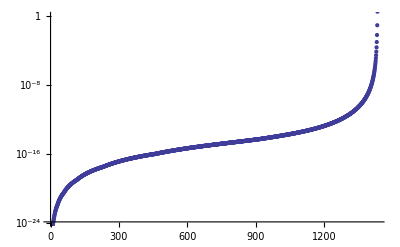

```mathematica
list = <<../src_ocaml/pped.dat;
volSet=Fold[pipeVolume[1,2,#1,#2]&,{}, list];
ListLogPlot[volSet[[1;;-2]]]
```

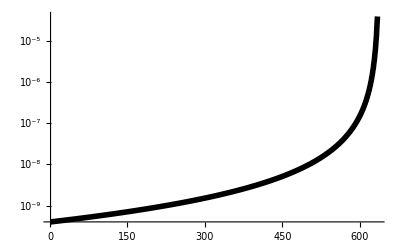

```mathematica
plot[<<disk-5.dat,Full]
```

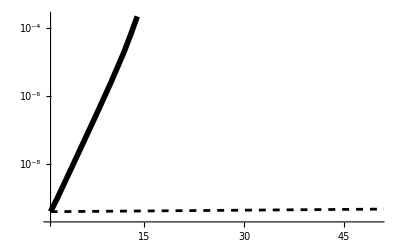

```mathematica
plotCompare[<<disk-5.dat,<<disk-5_box.dat,50]
```

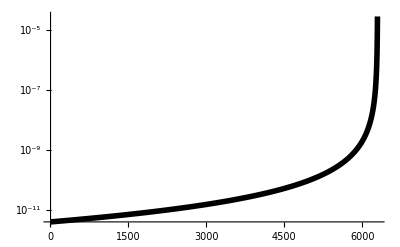

```mathematica
plot[<<disk-6.dat,Full]
```

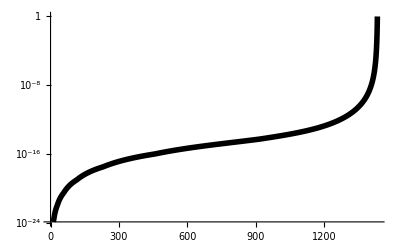

```mathematica
plot[<<bb-simple.dat]
```

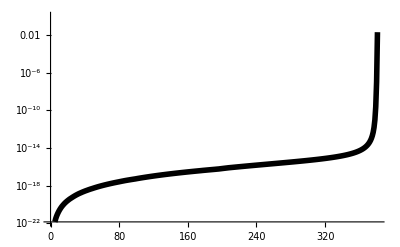

```mathematica
plot[<<bb-airfriction.dat]
```

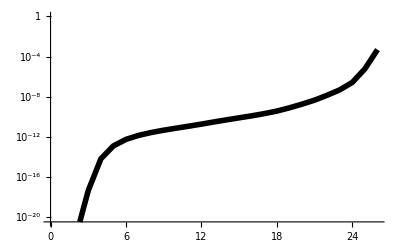

```mathematica
plot[<<bb-circle.dat]
```